# 4基盤ログの解析:推定ユーザーごとのアクセス推移（ユーザーストーリー）

-Graphics-

グラフ分析部分のみ、save済みグラフを読み込む。

## 準備

```mathematica
start=AbsoluteTime[Date[]]
```

3.91010975477347×10^9

#### 変数

```mathematica
date="20231020"
```

20231020

```mathematica
case={"ci","cs","la","wk"}
```

{ci,cs,la,wk}

```mathematica
base["ci"]="T=ci.P~5"
base["cs"]="T=cs.R=.P="
base["la"]="T=la.T~ea.A~hc.A~go.A~bot.P~api"
base["wk"]="T=wk.P~4.A~bot"
base["all"]="T=4"
```

T=ci.P~5

T=cs.R=.P=

T=la.T~ea.A~hc.A~go.A~bot.P~api

T=wk.P~4.A~bot

T=4

```mathematica
mountdir="/Volumes/home/NII/togo-log/rcoslogs/"
```

/Volumes/home/NII/togo-log/rcoslogs/

```mathematica
vocdir=mountdir<>"voc"
```

/Volumes/home/NII/togo-log/rcoslogs/voc

#### 解析用データ

```mathematica
fileliststr=Import[mountdir<>"log/D="<>date<>"/"<>"filenames","String"]
```

log-20231020.rcoslog0003.log

```mathematica
filelist=StringSplit[fileliststr]
```

{log-20231020.rcoslog0003.log}

元ログの大きさ （wc）

```mathematica
logwc=Import[mountdir<>"log/D="<>date<>"/logfiles.wc","String"]
```

20494709 284612363 9455761379 log-20231020.rcoslog0003.log

```mathematica
ckanfile=mountdir<>"crid/CIRDEV-1067_crid_list/ckan_product_crid_list.txt"
```

/Volumes/home/NII/togo-log/rcoslogs/crid/CIRDEV-1067_crid_list/ckan_product_crid_list.txt

```mathematica
ckanSt=Import[ckanfile,"String"];
```

```mathematica
(ckanName=StringSplit[ckanSt,"\n"])//Dimensions
```

{92643}

```mathematica
(ckanCridAC=Apply[Association,Map[#->#&,ckanName]])//Dimensions
```

{92643}

#### プログラム

vertexを指定してdirected-edgeを辿る部分グラフ抽出の関数：

```mathematica
directedConnectedGraphComponent[g_,v_]:=Module[{vAll,vOther,addEdge},
vAll=VertexList[g];
vOther=Complement[vAll,{v}];
addEdge=Map[#->v&,vOther];
Subgraph[g,ConnectedComponents[Flatten[{EdgeList[g],addEdge},1],v][[1]]]
]
```

グラフよりinがないノードを検出してそこから(g,v)に対して上記関数をアプライする関数：

```mathematica
vertexInGraph[g_Graph]:=Module[{deg,pos,vname},
deg=VertexInDegree[g];
pos=Position[deg,0]//Flatten//Union;
vname=VertexList[g][[pos]];
Map[directedConnectedGraphComponent[g,#]&,vname]
]
vertexInGraph[g_Integer]:=g
```

story-group-indexを各グラフにdistributeする関数：

```mathematica
distributeIdxGr[idxGr_]:=Module[
{date,idx,gr},
date=idxGr[[1]];
idx=idxGr[[2]];
gr=idxGr[[3]];
Map[{date,idx,#}&,gr]
]
```

stringからfqdnのみ抽出する関数：

```mathematica
fqdnFromPath[s_]:=StringJoin[StringSplit[s,"/"]⟦{1,3}⟧]
```

```mathematica
fqdnFromGraph[g_Graph]:=Union[Sort[Map[fqdnFromPath,VertexList[g]]]]
```

## Analysis

### Get graph

```mathematica
savedir=mountdir<>"log/D="<>date<>"/T=4/_story"
```

/Volumes/home/NII/togo-log/rcoslogs/log/D=20231020/T=4/_story

```mathematica
Get[savedir<>"/storyGrIdxFlDs3.save"];
```

### Analysis 1 graph property

基本属性

エッジ:

```mathematica
(eltbl[4]=Table[EdgeList[storyGrIdxFlDs3[4][[i]][[3]]],{i,Length[storyGrIdxFlDs3[4]]}])//Dimensions
```

{181351}

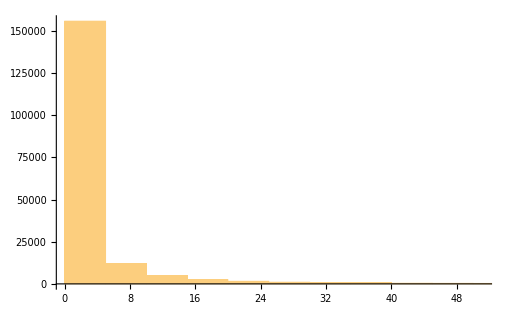

```mathematica
Histogram[Map[Length,eltbl[4]],{5}]
```

ノード:

```mathematica
(vltbl[4]=Table[VertexList[storyGrIdxFlDs3[4][[i]][[3]]],{i,Length[storyGrIdxFlDs3[4]]}])//Dimensions
```

{181351}

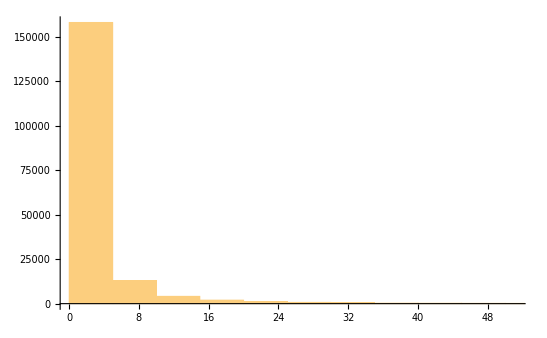

```mathematica
Histogram[Map[Length,vltbl[4]],{5}]
```

アクセス時刻:

```mathematica
(acct[4]=Map[#[[3,1]]&,eltbl[4],{2}])//Dimensions
```

{181351}

滞留時間：

```mathematica
(accspanMin[4]=Map[Max[#]-Min[#]&,acct[4]]/60)//Dimensions
```

{181351}

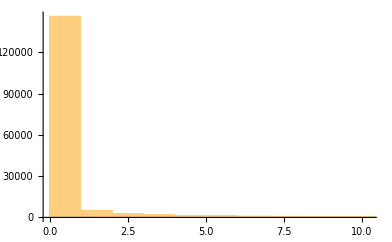

```mathematica
Histogram[accspanMin[4],{1}]
```

スタートノードが最小時刻になっていない。調整が必要か？

E/V ratio:

```mathematica
(ratioEV[4]=Map[Length,eltbl[4]]/Map[Length,vltbl[4]]//N)//Dimensions
```

{181351}

TV ratio :

```mathematica
(ratioTV[4]=acct[4]/Map[Length,vltbl[4]])//Dimensions
```

{181351}

TE ratio:

```mathematica
(ratioTE[4]=acct[4]/Map[Length,eltbl[4]])//Dimensions
```

{181351}

### Analysis 2 base interaction

リクエストパスから基盤名だけをとりだし、基盤連携を見る。

```mathematica
(GrBases[4]=Map[fqdnFromGraph[#[[3]]]&,storyGrIdxFlDs3[4]])//Dimensions
```

Part::partw: Part {1,3} of {cir.nii.ac.jp} does not exist.

StringJoin::string: String expected at position 1 in StringJoin[{cir.nii.ac.jp}⟦{1,3}⟧].

Part::partw: Part {1,3} of {} does not exist.

StringJoin::string: String expected at position 1 in StringJoin[{}⟦{1,3}⟧].

Part::partw: Part {1,3} of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

StringJoin::string: String expected at position 1 in StringJoin[{}⟦{1,3}⟧].

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

{181351}

NII基盤(4基盤以外も)へのアクセスを見る。

```mathematica
niidnpos=Flatten[Position[Map[StringMatchQ[#,RegularExpression[".*nii.ac.jp.*"]]||StringMatchQ[#,RegularExpression[".*jdcat.jsps.go.jp.*"]]&,Flatten[GrBases[4]]//Union],True]]
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{}⟦{1,3}⟧],RegularExpression[.*nii.ac.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{}⟦{1,3}⟧],RegularExpression[.*jdcat.jsps.go.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{cir.nii.ac.jp}⟦{1,3}⟧],RegularExpression[.*nii.ac.jp.*]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

{32,39,40,58,72,77,171,182,183,198,229,230,231,232,234,235,236,237,273,274,302,309,326,327,363,387,389,414,418,428,435,459,593,633,680,686,693,782,784,819,821,824,1045,1054,1083,1137,1425,1521}

```mathematica
(Flatten[GrBases[4]]//Union)[[niidnpos]]
```

{http:binder.cs.rcos.nii.ac.jp,http:ci.nii.ac.jp,http:cir.nii.ac.jp,http:grafana.cs.rcos.nii.ac.jp,http:jdcat.jsps.go.jp,http:kaken.nii.ac.jp,https:analytics.la.lms.nii.ac.jp,https:auth-cir.nii.ac.jp,https:auth.cir.nii.ac.jp,https:binder.cs.rcos.nii.ac.jp,https:ci.nii.ac.jp,https:ci.nii.ac.jp:443,https:ci-nii-ac-jp.kwansei.remotexs.co,https:ci-nii-ac-jp.libproxy.ouj.ac.jp,https:cir.nii.ac.jp,https:cir-nii-ac-jp.musashino-u.remotexs.co,https:cir-nii-ac-jp.nanzan-u.idm.oclc.org,https:cir-nii-ac-jp.translate.goog,https:dsc.repo.nii.ac.jp,https:ds.gakunin.nii.ac.jp,https:feedback.cir.nii.ac.jp,https:fukuoka-u.repo.nii.ac.jp,https:ge.nii.ac.jp,https:ge.nii.ac.jp:443,https:hosei.repo.nii.ac.jp,https:idp.nii.ac.jp,https:idp.rdm.nii.ac.jp,https:jdcat.jsps.go.jp,https:joshibi.repo.nii.ac.jp,https:jupyter.cs.rcos.nii.ac.jp,https:kaken.nii.ac.jp,https:kobegakuin.repo.nii.ac.jp,https:lms.nii.ac.jp,https:meatwiki.nii.ac.jp,https:niph.repo.nii.ac.jp,https:nrid.nii.ac.jp,https:office.gakunin.nii.ac.jp,https:openidp.nii.ac.jp,https:operationhub.cs.rcos.nii.ac.jp,https:rcos.nii.ac.jp,https:rdm.nii.ac.jp,https:repository.nii.ac.jp,https:stars.repo.nii.ac.jp,https:support.nii.ac.jp,https:toyo-bunko.repo.nii.ac.jp,https:wiki.nii.ac.jp,https:www.nii.ac.jp,https:www.unii.ac.jp}

```mathematica
niigrp=".*\\.nii\\.ac\\.jp.*"
```

.*\.nii\.ac\.jp.*

```mathematica
(GrNiiBases[4]=Map[Cases[#,x_/;StringMatchQ[x,RegularExpression[niigrp]]||StringMatchQ[x,RegularExpression[".*jdcat.jsps.go.jp.*"]]]&,GrBases[4]])//Dimensions
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{cir.nii.ac.jp}⟦{1,3}⟧],RegularExpression[.*\.nii\.ac\.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{cir.nii.ac.jp}⟦{1,3}⟧],RegularExpression[.*jdcat.jsps.go.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{}⟦{1,3}⟧],RegularExpression[.*\.nii\.ac\.jp.*]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

{181351}

```mathematica
Map[Length,GrBases[4]]//Tally
```

{{2,162039},{1,19304},{3,8}}

```mathematica
Map[Length,GrNiiBases[4]]//Tally
```

{{1,123782},{2,57569}}

```mathematica
(GrBasesTly[4]=Tally[GrBases[4]])//Dimensions
```

{1661,2}

```mathematica
(GrNiiBasesTly[4]=Tally[GrNiiBases[4]])//Dimensions
```

{50,2}

```mathematica
GrNiiBasesTly[4]//TableForm
```

https:cir.nii.ac.jp | 123419
https:ci.nii.ac.jp
https:cir.nii.ac.jp | 25840
http:ci.nii.ac.jp
https:cir.nii.ac.jp | 28517
https:cir.nii.ac.jp
https:support.nii.ac.jp | 107
https:jupyter.cs.rcos.nii.ac.jp | 162
https:jupyter.cs.rcos.nii.ac.jp
https:rdm.nii.ac.jp | 10
https:jupyter.cs.rcos.nii.ac.jp
https:openidp.nii.ac.jp | 12
https:ci.nii.ac.jp:443
https:cir.nii.ac.jp | 1779
http:cir.nii.ac.jp
https:cir.nii.ac.jp | 31
https:jdcat.jsps.go.jp | 55
http:binder.cs.rcos.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 1
https:auth.cir.nii.ac.jp
https:cir.nii.ac.jp | 11
https:cir.nii.ac.jp
https:dsc.repo.nii.ac.jp | 2
https:lms.nii.ac.jp | 146
https:cir.nii.ac.jp
https:repository.nii.ac.jp | 2
https:cir.nii.ac.jp
https:kaken.nii.ac.jp | 865
https:cir.nii.ac.jp
https:nrid.nii.ac.jp | 306
http:kaken.nii.ac.jp
https:cir.nii.ac.jp | 1
https:binder.cs.rcos.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 13
https:idp.rdm.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 5
https:jdcat.jsps.go.jp
https:jupyter.cs.rcos.nii.ac.jp | 1
https:cir.nii.ac.jp
https:www.nii.ac.jp | 8
https:idp.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 2
https:cir.nii.ac.jp
https:jdcat.jsps.go.jp | 7
https:lms.nii.ac.jp
https:rcos.nii.ac.jp | 1
https:cir.nii.ac.jp
https:fukuoka-u.repo.nii.ac.jp | 2
https:cir.nii.ac.jp
https:office.gakunin.nii.ac.jp | 1
https:cir.nii.ac.jp
https:lms.nii.ac.jp | 6
https:analytics.la.lms.nii.ac.jp
https:lms.nii.ac.jp | 7
https:ds.gakunin.nii.ac.jp
https:lms.nii.ac.jp | 1
https:idp.nii.ac.jp
https:lms.nii.ac.jp | 3
https:lms.nii.ac.jp
https:wiki.nii.ac.jp | 1
https:cir.nii.ac.jp
https:hosei.repo.nii.ac.jp | 1
http:grafana.cs.rcos.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 8
https:jupyter.cs.rcos.nii.ac.jp
https:operationhub.cs.rcos.nii.ac.jp | 1
https:cir.nii.ac.jp
https:feedback.cir.nii.ac.jp | 1
https:lms.nii.ac.jp
https:openidp.nii.ac.jp | 2
https:cir.nii.ac.jp
https:stars.repo.nii.ac.jp | 1
https:jdcat.jsps.go.jp
https:rcos.nii.ac.jp | 1
https:cir.nii.ac.jp
https:kobegakuin.repo.nii.ac.jp | 1
https:jdcat.jsps.go.jp
https:support.nii.ac.jp | 1
https:lms.nii.ac.jp
https:www.nii.ac.jp | 2
https:lms.nii.ac.jp
https:meatwiki.nii.ac.jp | 1
https:cir.nii.ac.jp
https:niph.repo.nii.ac.jp | 1
http:jdcat.jsps.go.jp
https:jdcat.jsps.go.jp | 1
https:cir.nii.ac.jp
https:joshibi.repo.nii.ac.jp | 1
https:cir.nii.ac.jp
https:toyo-bunko.repo.nii.ac.jp | 1
https:cir.nii.ac.jp
https:ge.nii.ac.jp | 1
https:cir.nii.ac.jp
https:ge.nii.ac.jp:443 | 1
https:auth-cir.nii.ac.jp
https:cir.nii.ac.jp | 1

グラフが多すぎるので選び方を考え中。

ここから、Idpで認証されたログはIdpがリファラーとして入ってくるが、認証元情報がはいらないため基盤連携のグラフに組み込まれない。
 一方で、Idpを遮蔽して認証元からアクセス先へのエッジは発生する。

### Analysis 3 time series

```mathematica
accessFirst=(Cases[accessTime[4],x_/;x>0]//Min)
```

3.90673×10^9

```mathematica
accessLast=(Cases[accessTime[4],x_/;x>0]//Max)
```

3.90684×10^9

```mathematica
Sort[accessTime["ci"]]//Length
```

3849090

```mathematica
BC600["ci"]=BinCounts[Sort[accessTime["ci"]],{accessFirst,accessLast,60*10}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,9420,20190,18666,18836,22967,24212,25732,23769,23170,24903,23728,26157,29178,33924,32447,29631,34027,33023,32603,33295,31366,31320,31669,30610,31589,33265,35663,34961,36487,36369,37028,36506,32986,33714,36344,35290,29927,37195,37516,36990,37239,36436,36106,36712,36819,35637,35251,33760,32843,30659,19533,27919,29452,20057,30301,21047,16874,20830,19144,20893,22006,25253,22497,22070,25866,25566,28322,30304,30425,29390,27014,27183,27363,25165,25939,24680,22830,21337,20744,24621,23096,24672,27300,27300,26472,26799,24406,22874,24294,21843,23831,22953,29426,26284,27587,28193,24405,25146,27935,26317,23703,31070,31395,31654,31999,31007,30055,30136,28962,28768,31443,26320,26332,26009,22721,24903,24305,24185,24042,22742,21257,22744,20957,20510,20138,21432,20108,21435,20377,19625,19786,19997,17309,17392,17957,17860,16827,17447,18309,18912,22170,23324,22684,22619}

```mathematica
BC600["cs"]=BinCounts[Sort[accessTime["cs"]],{accessFirst,accessLast,60*10}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,299,201,769,621,242,41,133,300,273,141,62,68,61,7,6,28,5,40,18,4,4,22,4,11,4,7,7,21,2,46,2,3,4,18,2,2,3,5,2,19,0,60,0,5,2,22,2,21,3,1,73,421,137,90,76,48,5,135,220,102,125,18,82,93,60,309,636,854,1132,921,799,939,1101,357,613,642,808,710,507,355,267,321,856,626,827,952,779,576,418,480,256,584,2752,1132,1521,575,1355,849,77,147,18,424,23,319,494,455,462,42,312,657,65,42,162,42,95,2,96,202,3,8,3,37,1,17,8,183,10,67,3,23,0,8,0,5,0,19,0,47,1,12,0,25,1,3}

```mathematica
BC600["la"]=BinCounts[Sort[accessTime["la"]],{accessFirst,accessLast,60*10}]
```

{2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,101,35,2,30,13,0,3,0,6,111,26,3,3,1,19,8,26,0,5,0,0,1,4,4,1,4,3,6,3,0,0,1,3,0,8,3,1,2,0,180,10,64,8,0,0,2,42,13,93,36,111,0,23,4,56,26,21,1,45,95,0,2,0,48,18,2,66,49,0,50,47,47,64,286,296,253,288,197,38,77,55,80,183,101,45,0,80,77,91,41,65,73,171,81,2,118,259,191,152,134,162,333,49,90,392,83,200,24,46,4,1,1,4,1,11,5,13,19,1,0,186,0,0,3,3,1,1,3,0,0,0,0,43,17,15,1,3,35,2,3,93,4,1}

```mathematica
BC600["wk"]=BinCounts[Sort[accessTime["wk"]],{accessFirst,accessLast,60*10}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,8,0,1,1,0,1,0,1,7,0,0,0,1,0,0,0,0,18,2,11,8,4,4,1,1,1,0,0,0,5,2,3,7,0,0,0,0,2,0,0,2,2,4,2,0,2,0,23,3,0,1,1,8,4,16,4,13,11,5,2,11,10,8,4,30,10,0,0,5,2,0,12,2,3,7,1,2,0,0,15,12,8,12,21,0,120,13,9,22,0,28,0,1,1,0,0,0,6,54,9,0,1,18,1,1,9,1,1,1,2,2,2,0,0,1,0,0,0,28,0,0,0,0,1,1,0,1,2,0,18,6,0,0,0,0,1,1,0,0,0,1,0,1}

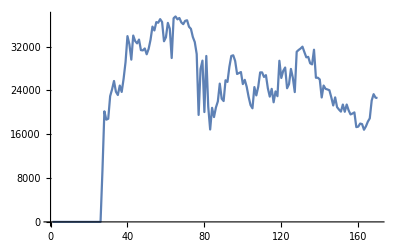

```mathematica
ListPlot[BC600["ci"],PlotRange->Full,Joined->True]
```

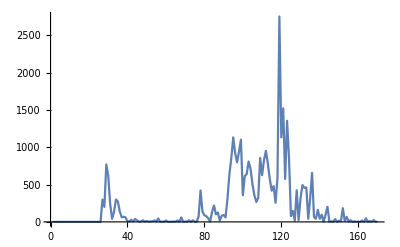

```mathematica
ListPlot[BC600["cs"],PlotRange->Full,Joined->True]
```

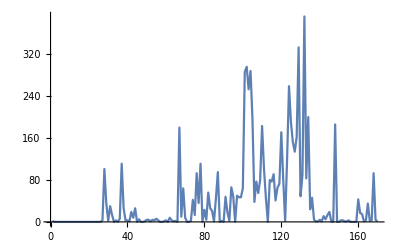

```mathematica
ListPlot[BC600["la"],PlotRange->Full,Joined->True]
```

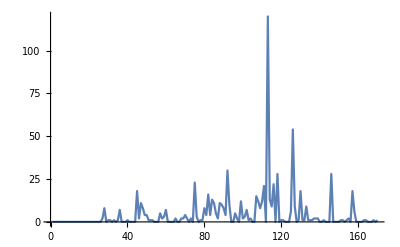

```mathematica
ListPlot[BC600["wk"],PlotRange->Full,Joined->True]
```

### Analysis 4 CKAN impact

ckanCRIDを含むグラフを抽出する。

すでに構成したハッシュとグラフのプロパティを当てる関数。ひとつでもあたればTrueを返す。
 ハッシュはログ中の位置を記述しており、リクエストパス・リファラーを分けたもの、Unionしたもの。

滞留時間をグラフから得る関数：

```mathematica
stayTime[g_Graph]:=Module[{elist,tlist},
elist=EdgeList[g];
tlist=Map[#[[3,1]]&,elist];
Max[tlist]-Min[tlist]
]
```

ckanCRIDを含むログの行とグラフのエッジにあるログの行を当てる関数 （T/F）:

```mathematica
logGraphQ[gr_Graph,asc_Association]:=Module[{elist,logposlist,res},
elist=EdgeList[gr];
logposlist=Map[#[[3,2]]&,elist];
res=Map[asc[#]&,logposlist];
Position[res,_Integer,{1}]/.{{}->False,{__}->True}
]
```

ckanCRIDをリクエストに含むノードをハイライトする関数：

```mathematica
toCRID[s_String/;StringMatchQ[s,RegularExpression["https://cir.nii.ac.jp/crid/.*"]]]:=StringTake[StringSplit[s,"/"][[5]],19]
```

```mathematica
ckanVertexHighlihgt[g_Graph,asc_Association]:=Module[{vlist,pos,targetv,op},
vlist=VertexList[g];
pos=Flatten[Position[Map[ckanCridPRACQ[toCRID[#]]&,VertexList[g]],True]];
targetv=vlist[[pos]];
op=VertexStyle->Map[#->Red&,targetv];
Graph[g,op]
]
```

CKAN - CRIDを含むグラフの抽出

```mathematica
(ckanGrP[4]=Map[If[logGraphQ[#[[3]],ckanCridPLogPosAC[4]],#,Null]&,storyGrIdxFlDs3[4]])//Dimensions
```

{181351}

```mathematica
(ckanGrR[4]=Map[If[logGraphQ[#[[3]],ckanCridRLogPosAC[4]],#,Null]&,storyGrIdxFlDs3[4]])//Dimensions
```

{181351}

```mathematica
(ckanGrPR[4]=Map[If[logGraphQ[#[[3]],ckanCridPRLogPosAC[4]],#,Null]&,storyGrIdxFlDs3[4]])//Dimensions
```

{181351}

```mathematica
(ckanGrPsel[4]=Cases[ckanGrP[4],{__},{1}])//Dimensions
```

{77,3}

```mathematica
ckanGrPselVL[4]=Map[VertexList[#[[3]]]&,ckanGrPsel[4]];
```

```mathematica
ckanGrPselEL[4]=Map[EdgeList[#[[3]]]&,ckanGrPsel[4]];
```

```mathematica
(ckanGrRsel[4]=Cases[ckanGrR[4],{__},{1}])//Dimensions
```

{12,3}

```mathematica
ckanGrRselVL[4]=Map[VertexList[#[[3]]]&,ckanGrRsel[4]];
```

```mathematica
ckanGrRselEL[4]=Map[EdgeList[#[[3]]]&,ckanGrRsel[4]];
```

```mathematica
(ckanGrPRsel[4]=Cases[ckanGrPR[4],{__},{1}])//Dimensions
```

{77,3}

```mathematica
ckanGrPRselVL[4]=Map[VertexList[#[[3]]]&,ckanGrPRsel[4]];
```

```mathematica
ckanGrPRselEL[4]=Map[EdgeList[#[[3]]]&,ckanGrPRsel[4]];
```

```mathematica
(ckanGrPRselHL[4]=Map[{#[[1]],#[[2]],ckanVertexHighlihgt[#[[3]],ckanCridPRACQ]}&,ckanGrPRsel[4]])//Dimensions
```

{77,3}

```mathematica
ckanGrPRVcount[4]=Map[VertexCount[#[[3]]]&,ckanGrPRselHL[4]]
```

{2,2,6,13,38,16,32,47,15,15,27,52,8,73,72,38,16,27,16,9,9,65,19,12,7,19,125,126,140,127,2,63,187,186,185,15,9,31,31,31,38,4,46,10,11,4,670,47,110,43,26,133,165,133,7,79,13,17,61,66,64,125,104,126,5,239,245,240,238,2,75,22,73,74,6,3,12}

```mathematica
accTimeList[g_Graph]:=Module[{elist,tlist},
elist=EdgeList[g];
tlist=Sort[Map[#[[3,1]]&,elist],#1>#2&]
]
```

```mathematica
timeSpan[tlist_]:=Map[(#[[1]]-#[[2]])&,Partition[tlist,2,1]]
```

```mathematica
ckanGrPRstayTime[4]=Map[stayTime[#[[3]]]&,ckanGrPRselHL[4]]
```

{0.,0.,207.,241.,8432.,746.,3793.,5928.,300.,1304.,759.,1871.,96.,26394.,7513.,3748.,4021.,911.,2775.,1570.,1125.,1978.,4219.,532.,121.,474.,43057.,39209.,40489.,39209.,0.,2738.,16958.,8230.,8230.,1554.,1225.,2000.,2000.,2000.,27097.,18.,18165.,2154.,534.,23.,24681.,30964.,48534.,2427.,10808.,21870.,29236.,21870.,146.,9392.,1265.,5418.,2415.,5558.,5525.,6123.,5205.,6123.,9752.,4516.,4535.,4516.,4516.,0.,6131.,1518.,13194.,13194.,580.,12.,192.}

### Analysis 5 CKAN graph reform

program :

可能な全Vertexにアクセス時間リストを付与：

```mathematica
gatherDistributeUniq[l_]:=Module[{first,target},
first=l[[1,1]];
target=Map[#[[2]]&,l];
{first,target}
]
```

```mathematica
gatherDistributeUniqRl[l_]:=Module[{first,target},
first=l[[1,1]];
target=Map[#[[2]]&,l];
first->{first,target}
]
```

```mathematica
addVertexAccTime[g_]:=Module[{gatherTimeV,gatherTimeVRl},
gatherTimeV=Gather[Map[{#[[2]],#[[3,1]]}&,EdgeList[g]],#1[[1]]==#2[[1]]&];
gatherTimeVRl=Map[gatherDistributeUniqRl,gatherTimeV];
VertexReplace[g,gatherTimeVRl]
]
```

```mathematica
guessVertexCoorGr[g_,timeshift_]:=Module[{allAccTime,baseTime,repPos,target,repRl},
allAccTime=Cases[Flatten[Map[#[[2]]&,g//VertexList]],_Real];
baseTime=Min[allAccTime]+timeshift;
repPos=Flatten[Position[Map[Head,VertexList[g]],String]];
target=Map[VertexList[g][[#]]&,repPos];
repRl=Map[#->{#,{baseTime}}&,target];
VertexReplace[g,repRl]
]
```

```mathematica
accTimeMinGr[g_]:=Min[Cases[Flatten[Map[#[[2]]&,g//VertexList]],_Real]]
```

```mathematica
reformCoorGr[g_,baseTime_,f_]:=f[Map[{Max[#[[2]]],Min[#[[2]]]}&,VertexList[g]]-baseTime]
```

```mathematica
timeLineGr[g_,timeshift_,f_]:=Module[{gnew,btime,coornew},
gnew=guessVertexCoorGr[g,timeshift];
btime=accTimeMinGr[gnew];
coornew=reformCoorGr[gnew,btime,Sqrt];
Graph[gnew,VertexSize->Automatic,VertexCoordinates->coornew]
]
```

```mathematica
(ckanGrPRselHLAT[4]=Map[{#[[1]],#[[2]],addVertexAccTime[#[[3]]]}&,ckanGrPRselHL[4]])//Dimensions
```

{77,3}

ロググループ：

```mathematica
loggroupCKAN=Map[#[[2]]&,ckanGrPRselHLAT[4]]
```

{{1157,1},{1419,1},{3640,1},{4374,1},{5337,1},{11484,1},{15808,1},{19161,1},{20222,1},{22425,1},{24468,1},{25470,1},{26639,1},{28414,1},{28414,1},{33776,1},{36066,1},{41476,1},{47181,1},{49150,1},{49150,1},{52106,1},{52440,1},{57286,1},{57694,1},{61150,1},{61320,1},{61320,1},{61320,1},{61320,1},{66188,1},{66599,1},{68102,1},{68102,1},{68102,1},{70938,1},{70938,1},{72201,1},{72201,1},{72201,1},{72537,1},{81509,1},{81991,1},{84271,1},{84468,1},{86982,1},{87052,1},{89634,1},{90349,1},{90583,1},{91568,1},{94172,1},{94172,1},{94172,1},{94238,1},{94636,1},{94996,1},{99074,1},{99168,1},{101749,1},{101749,1},{106430,1},{106430,1},{106430,1},{107652,1},{110002,1},{110002,1},{110002,1},{110002,1},{123762,1},{126392,1},{129396,1},{132602,1},{132602,1},{132815,1},{137365,1},{138261,1}}

ノードの数え上げ：

```mathematica
vcCKAN=Map[VertexCount[#[[3]]]&,ckanGrPRselHLAT[4]]
```

{2,2,6,13,38,16,32,47,15,15,27,52,8,73,72,38,16,27,16,9,9,65,19,12,7,19,125,126,140,127,2,63,187,186,185,15,9,31,31,31,38,4,46,10,11,4,670,47,110,43,26,133,165,133,7,79,13,17,61,66,64,125,104,126,5,239,245,240,238,2,75,22,73,74,6,3,12}

エッジの数え上げ：

```mathematica
ecCKAN=Map[EdgeCount[#[[3]]]&,ckanGrPRselHLAT[4]]
```

{1,1,10,15,77,23,39,78,24,22,38,81,13,117,122,49,27,61,17,16,14,82,26,16,8,31,195,176,210,180,1,88,352,293,283,36,20,73,73,73,46,4,53,19,16,3,1153,75,171,78,37,160,220,165,7,148,18,26,92,177,127,204,174,205,5,403,433,407,404,1,116,20,79,81,7,2,14}

アクセス時刻：

```mathematica
(accCKAN=Map[Map[#[[3,1]]&,EdgeList[#[[3]]]]&,ckanGrPRselHLAT[4]])//Dimensions
```

{77}

最大滞在時間：

```mathematica
maxTimeSpan[l_]:=Max[Map[#[[1]]-#[[2]]&,Partition[Sort[l,#1>#2&],2,1]]]
```

```mathematica
(maxtimespanCKAN=Map[maxTimeSpan,accCKAN]/.{-Infinity->0})/60
```

{0,0,1.15,0.616667,87.9833,7.56667,34.6833,54.15,0.816667,16.7167,6.88333,5.5,0.483333,314.217,80.6333,25.6,52.0167,4.71667,39.3833,13.85,13.85,5.76667,54.4,1.48333,0.733333,0.95,125.167,126.083,66.2833,126.083,0,4.51667,128.767,84.2,84.2,11.95,11.95,6.11667,6.11667,6.11667,429.683,0.15,218.167,27.9,3.5,0.266667,99.4,219.833,131.55,9.65,77.3167,74.0333,67.8667,74.0333,0.733333,66.4833,14.5667,49.3167,9.55,29.2667,29.7333,18.8667,18.2167,18.8667,64.1167,11.0833,11.0833,11.0833,11.0833,0,26.9333,10.2667,68.85,68.85,9.31667,0.2,0.716667}

滞留時間：

```mathematica
staytimeCKAN=Map[Max[#]-Min[#]&,accCKAN]
```

{0.,0.,207.,241.,8432.,746.,3793.,5928.,300.,1304.,759.,1871.,96.,26394.,7513.,3748.,4021.,911.,2775.,1570.,1125.,1978.,4219.,532.,121.,474.,43057.,39209.,40489.,39209.,0.,2738.,16958.,8230.,8230.,1554.,1225.,2000.,2000.,2000.,27097.,18.,18165.,2154.,534.,23.,24681.,30964.,48534.,2427.,10808.,21870.,29236.,21870.,146.,9392.,1265.,5418.,2415.,5558.,5525.,6123.,5205.,6123.,9752.,4516.,4535.,4516.,4516.,0.,6131.,1518.,13194.,13194.,580.,12.,192.}

```mathematica
staytimeCKAN/60
```

{0.,0.,3.45,4.01667,140.533,12.4333,63.2167,98.8,5.,21.7333,12.65,31.1833,1.6,439.9,125.217,62.4667,67.0167,15.1833,46.25,26.1667,18.75,32.9667,70.3167,8.86667,2.01667,7.9,717.617,653.483,674.817,653.483,0.,45.6333,282.633,137.167,137.167,25.9,20.4167,33.3333,33.3333,33.3333,451.617,0.3,302.75,35.9,8.9,0.383333,411.35,516.067,808.9,40.45,180.133,364.5,487.267,364.5,2.43333,156.533,21.0833,90.3,40.25,92.6333,92.0833,102.05,86.75,102.05,162.533,75.2667,75.5833,75.2667,75.2667,0.,102.183,25.3,219.9,219.9,9.66667,0.2,3.2}

```mathematica
f[x_]=Log[x+1]
```

Log[1+x]

```mathematica
(ckanGrPRselHLTL[4]=Map[timeLineGr[#[[3]],-60,f]&,ckanGrPRselHLAT[4]])//Dimensions
```

Part::partd: Part specification https://www.google.com/⟦2⟧ is longer than depth of object.

Part::partd: Part specification https://www.bing.com/⟦2⟧ is longer than depth of object.

Part::partd: Part specification https://search.yahoo.co.jp/⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{77}

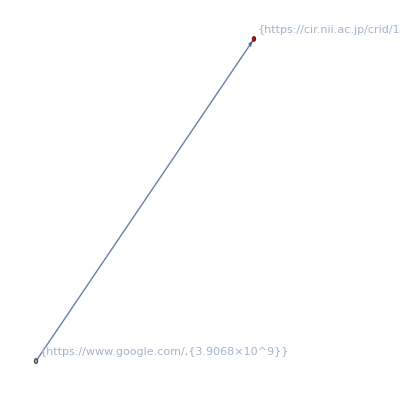

```mathematica
ckanGrPRselHLTL[4][[1]]
```

### Analysis 6 CKAN voc-graph

vocRlの読み込み：

```mathematica
vocRlFiles=FileNames[vocdir<>"/*.wl"]
```

{/Volumes/home/NII/togo-log/rcoslogs/voc/voc_path_action_ci_rl.wl,/Volumes/home/NII/togo-log/rcoslogs/voc/voc_path_action_cs_rl.wl,/Volumes/home/NII/togo-log/rcoslogs/voc/voc_path_action_la_rl.wl,/Volumes/home/NII/togo-log/rcoslogs/voc/voc_path_action_wk_rl.wl,/Volumes/home/NII/togo-log/rcoslogs/voc/voc_ref_action_ci_rl.wl,/Volumes/home/NII/togo-log/rcoslogs/voc/voc_ref_action_cs_rl.wl,/Volumes/home/NII/togo-log/rcoslogs/voc/voc_ref_action_la_rl.wl,/Volumes/home/NII/togo-log/rcoslogs/voc/voc_ref_action_wk_rl.wl}

```mathematica
vocRlList=Map[Get,vocRlFiles];
```

```mathematica
(vocRl["all:path"]=Apply[Join,vocRlList])//Dimensions
```

{113}

```mathematica
vocRl["all:path"][[1]]
```

x_/;StringMatchQ[x,RegularExpression[https://cir.nii.ac.jp/]]→voc[ci:top]

===== /プログラム検討 =====

====== /引数 ======

```mathematica
gr=ckanGrPRselHLTL[4][[1]]
```

-Graphics-

```mathematica
rl=vocRl["all:path"];
```

====== 引数/ ======

====== /内部変数 ======

```mathematica
vl=VertexList[gr]
```

{{https://www.google.com/,{3.9068×10^9}},{https://cir.nii.ac.jp/crid/1690013498973410816,{3.9068×10^9}}}

```mathematica
vname=Map[#[[1]]&,vl]
```

{https://www.google.com/,https://cir.nii.ac.jp/crid/1690013498973410816}

```mathematica
vrename=(vname/.rl)
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/ja]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/\?.*]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

{https://www.google.com/,voc[ci:detail]}

```mathematica
vrenameRl=Map[Apply[Rule,#]&,Transpose[{vl,vrename}]]
```

{{https://www.google.com/,{3.9068×10^9}}→https://www.google.com/,{https://cir.nii.ac.jp/crid/1690013498973410816,{3.9068×10^9}}→voc[ci:detail]}

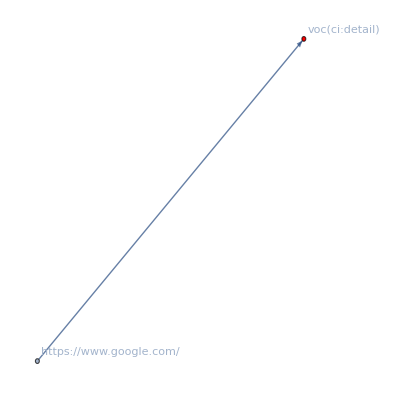

```mathematica
Graph[gr,VertexLabels->vrenameRl]
```

====== 内部変数/ ======

===== プログラム検討/ =====

```mathematica
toVocGraph[gr_,rl_]:=Module[{vl,vname,vrename,vrenameRl},
Print["it may cause StringMatchQ warn."];
vl=VertexList[gr];
vname=Map[#[[1]]&,vl];
vrename=(vname/.rl);
vrenameRl=Map[Apply[Rule,#]&,Transpose[{vl,vrename}]];
Graph[gr,VertexLabels->vrenameRl]
]
```

```mathematica
toVocGraph[ckanGrPRselHLTL[4][[1]],vocRl["all:path"]]
```

it may cause StringMatchQ warn.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/ja]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/\?.*]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

-Graphics-

it may cause StringMatchQ warn.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/ja]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/\?.*]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

it may cause StringMatchQ warn.

it may cause StringMatchQ warn.

it may cause StringMatchQ warn.

«73 more identical outputs»

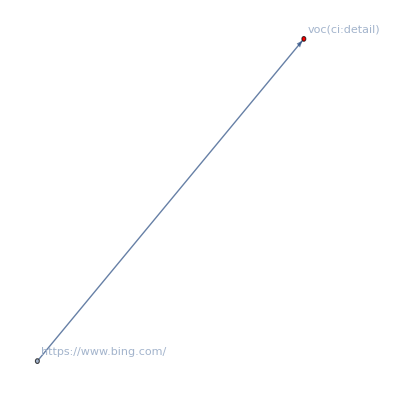
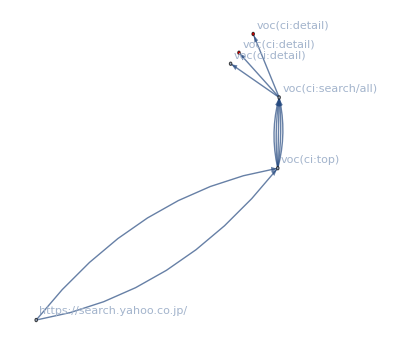
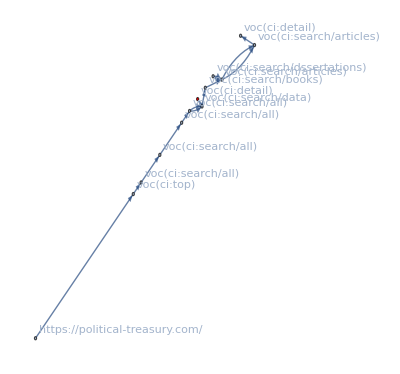
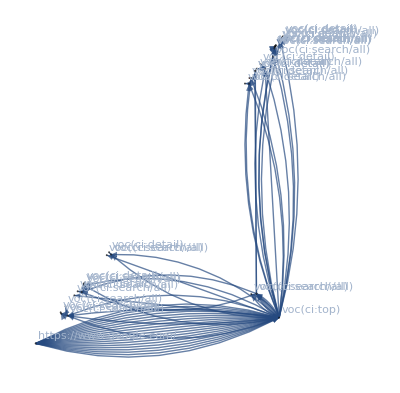
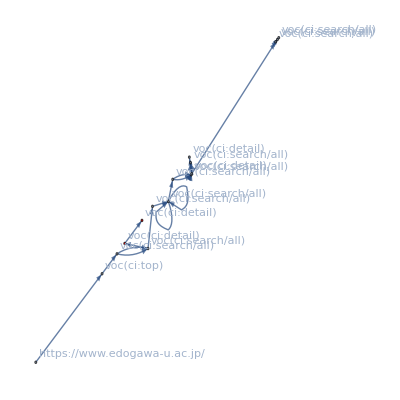
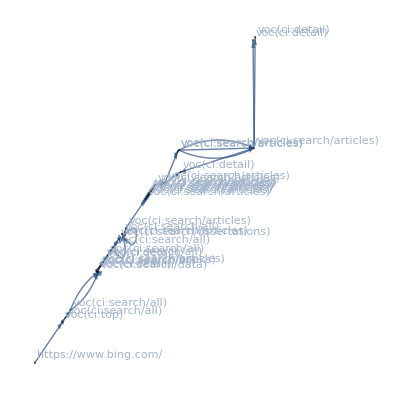
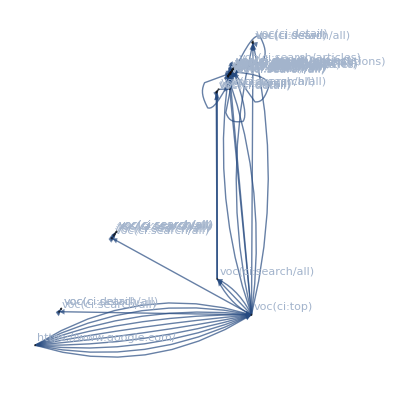
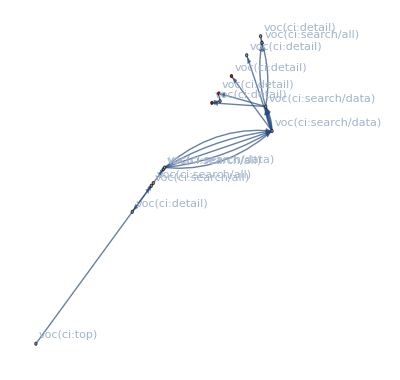
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
Map[toVocGraph[#,vocRl["all:path"]]&,ckanGrPRselHLTL[4]]//TableForm
```

### Report:CKAN impact

```mathematica
logtbl={{"- ログ件数 -","述べログ件数"},{{"全件数","ユーザーアクセス件数"},{ToExpression[StringSplit[logwc][[1]]],idxLogLen[4]}}}//TableForm
```

- ログ件数 - | 述べログ件数
全件数
ユーザーアクセス件数 | 20494709
3892534

```mathematica
ckanlogtbl={{"- CKAN-cridを含むログ件数 -","述べログ件数","cridのユニーク件数"},{{"リクエストにCKAN-crid含む","リファラーにCKAN-crid含む","いずれか含む"},{ckanCridPLogPos[4]//Length,ckanCridRLogPos[4]//Length,ckanCridPRLogPos[4]//Length},{Union[ckanCridPlist]//Length,Union[ckanCridRlist]//Length,ckanCridPRU//Length}}}//TableForm
```

- CKAN-cridを含むログ件数 - | 述べログ件数 | cridのユニーク件数
リクエストにCKAN-crid含む
リファラーにCKAN-crid含む
いずれか含む | 460
13
472 | 424
10
424

```mathematica
ckanchaintbl={{"- アクション連鎖数 -","件数"},{{"全件数","ノードにCKAN-crid含む"},{storyGrIdxFlDs3[4]//Length,ckanGrPRselHL[4]//Length}}}//TableForm
```

- アクション連鎖数 - | 件数
全件数
ノードにCKAN-crid含む | 181351
77

```mathematica
ckangrsummarytbl={{"アクセスグラフ通し番号","ロググループ","ノード数","エッジ数","最大滞在時間(分)","滞留時間(分)"},{Table[i,{i,Length[loggroupCKAN]}],loggroupCKAN,vcCKAN,ecCKAN,maxtimespanCKAN/60,staytimeCKAN/60}}//TableForm
```

アクセスグラフ通し番号 | ロググループ | ノード数 | エッジ数 | 最大滞在時間(分) | 滞留時間(分)
1
2
3
4
5
6
7
8
9
10
11
12
13
14
15
16
17
18
19
20
21
22
23
24
25
26
27
28
29
30
31
32
33
34
35
36
37
38
39
40
41
42
43
44
45
46
47
48
49
50
51
52
53
54
55
56
57
58
59
60
61
62
63
64
65
66
67
68
69
70
71
72
73
74
75
76
77 | 1157 | 1
1419 | 1
3640 | 1
4374 | 1
5337 | 1
11484 | 1
15808 | 1
19161 | 1
20222 | 1
22425 | 1
24468 | 1
25470 | 1
26639 | 1
28414 | 1
28414 | 1
33776 | 1
36066 | 1
41476 | 1
47181 | 1
49150 | 1
49150 | 1
52106 | 1
52440 | 1
57286 | 1
57694 | 1
61150 | 1
61320 | 1
61320 | 1
61320 | 1
61320 | 1
66188 | 1
66599 | 1
68102 | 1
68102 | 1
68102 | 1
70938 | 1
70938 | 1
72201 | 1
72201 | 1
72201 | 1
72537 | 1
81509 | 1
81991 | 1
84271 | 1
84468 | 1
86982 | 1
87052 | 1
89634 | 1
90349 | 1
90583 | 1
91568 | 1
94172 | 1
94172 | 1
94172 | 1
94238 | 1
94636 | 1
94996 | 1
99074 | 1
99168 | 1
101749 | 1
101749 | 1
106430 | 1
106430 | 1
106430 | 1
107652 | 1
110002 | 1
110002 | 1
110002 | 1
110002 | 1
123762 | 1
126392 | 1
129396 | 1
132602 | 1
132602 | 1
132815 | 1
137365 | 1
138261 | 1 | 2
2
6
13
38
16
32
47
15
15
27
52
8
73
72
38
16
27
16
9
9
65
19
12
7
19
125
126
140
127
2
63
187
186
185
15
9
31
31
31
38
4
46
10
11
4
670
47
110
43
26
133
165
133
7
79
13
17
61
66
64
125
104
126
5
239
245
240
238
2
75
22
73
74
6
3
12 | 1
1
10
15
77
23
39
78
24
22
38
81
13
117
122
49
27
61
17
16
14
82
26
16
8
31
195
176
210
180
1
88
352
293
283
36
20
73
73
73
46
4
53
19
16
3
1153
75
171
78
37
160
220
165
7
148
18
26
92
177
127
204
174
205
5
403
433
407
404
1
116
20
79
81
7
2
14 | 0
0
1.15
0.616667
87.9833
7.56667
34.6833
54.15
0.816667
16.7167
6.88333
5.5
0.483333
314.217
80.6333
25.6
52.0167
4.71667
39.3833
13.85
13.85
5.76667
54.4
1.48333
0.733333
0.95
125.167
126.083
66.2833
126.083
0
4.51667
128.767
84.2
84.2
11.95
11.95
6.11667
6.11667
6.11667
429.683
0.15
218.167
27.9
3.5
0.266667
99.4
219.833
131.55
9.65
77.3167
74.0333
67.8667
74.0333
0.733333
66.4833
14.5667
49.3167
9.55
29.2667
29.7333
18.8667
18.2167
18.8667
64.1167
11.0833
11.0833
11.0833
11.0833
0
26.9333
10.2667
68.85
68.85
9.31667
0.2
0.716667 | 0.
0.
3.45
4.01667
140.533
12.4333
63.2167
98.8
5.
21.7333
12.65
31.1833
1.6
439.9
125.217
62.4667
67.0167
15.1833
46.25
26.1667
18.75
32.9667
70.3167
8.86667
2.01667
7.9
717.617
653.483
674.817
653.483
0.
45.6333
282.633
137.167
137.167
25.9
20.4167
33.3333
33.3333
33.3333
451.617
0.3
302.75
35.9
8.9
0.383333
411.35
516.067
808.9
40.45
180.133
364.5
487.267
364.5
2.43333
156.533
21.0833
90.3
40.25
92.6333
92.0833
102.05
86.75
102.05
162.533
75.2667
75.5833
75.2667
75.2667
0.
102.183
25.3
219.9
219.9
9.66667
0.2
3.2

### Export:CKAN impact

```mathematica
(ckanEL=Map[MapApply[List,EdgeList[#]]&,ckanGrPRselHLTL[4]])//Dimensions
```

{77}

```mathematica
ckanELexp=Map[{#[[1,1]],#[[2,1]]}&,ckanEL,{2}];
```

```mathematica
expdir=mountdir<>"log/D="<>date<>"/T=4/_story"
```

/Volumes/home/NII/togo-log/rcoslogs/log/D=20231020/T=4/_story

```mathematica
SetDirectory[expdir]
```

/Volumes/home/NII/togo-log/rcoslogs/log/D=20231020/T=4/_story

```mathematica
Export["ckanedgelist.json",ckanELexp]
```

ckanedgelist.json

## 終端処理

```mathematica
end=AbsoluteTime[Date[]]
```

3.910109850101813×10^9

```mathematica
end-start
```

95.328343